```mathematica
(* Michael Barile 
STAT 786
HW #1 *)

(* Calculating lambda based off of given values of alpha, deltax and deltat *)
alpha=1/2;
deltax=.1;
deltat=.01;
lambda=alpha*deltat/deltax^2;
```

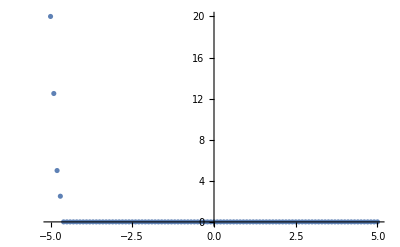

```mathematica
(* vector of x values from -5 to 5 in steps of deltax = 0.1 *)
xvec={-5};
x0=-5;
While[Max[xvec]<5,
x=x0+deltax;
AppendTo[xvec,x];
x0=x;
];
For[i=1,i≤Length[xvec],++i,
If[Abs[xvec[[i]]]<10^-5,
xvec[[i]]=0
];
];

(* temperature values along rod at time t = 0 *)
uvec={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[uvec,20],
AppendTo[uvec,0]
];
];

(* Constructing matrix A *)

A={};
For[i=1,i≤Length[xvec],++i,
inew={};
For[j=1,j≤Length[xvec],++j,
If[j==i,
AppendTo[inew,1-2*lambda],
If[j==i-1||j==i+1,
AppendTo[inew,lambda],
AppendTo[inew,0]
];
];
];
AppendTo[A,inew]
];

(* Constructing and replacing top and bottom rows in matrix A to fix the first and last entry of uvec *)

toprow={};
For[i=1,i≤Length[xvec],++i,
If[i==1,
AppendTo[toprow,1],
AppendTo[toprow,0]
];
];

bottomrow={};
For[i=1,i≤Length[xvec],++i,
If[i==Length[xvec],
AppendTo[bottomrow,1],
AppendTo[bottomrow,0]
];
];
A[[1]]=toprow;
A[[Length[xvec]]]=bottomrow;


(* temperature plotted as a function of position at time t = .03, .06, .08 and .10 *)

uvec3=uvec;
For[i=1,i≤3,++i,
unew=A.uvec3;
uvec3=unew
];

iter3={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter3,{xvec[[i]],uvec3[[i]]}]
];

ListPlot[iter3]

(* t = 0.03 *)
```

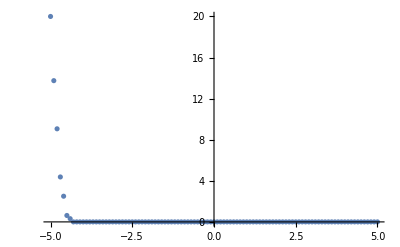

```mathematica
uvec6=uvec;
For[i=1,i≤6,++i,
unew=A.uvec6;
uvec6=unew
];

iter6={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter6,{xvec[[i]],uvec6[[i]]}]
];

ListPlot[iter6]

(* t = 0.06 *)
```

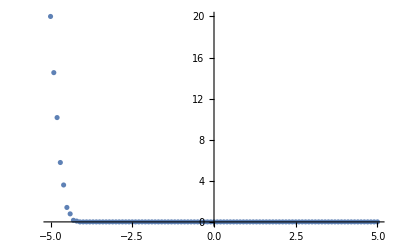

```mathematica
uvec8=uvec;
For[i=1,i≤8,++i,
unew=A.uvec8;
uvec8=unew
];

iter8={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter8,{xvec[[i]],uvec8[[i]]}]
];

ListPlot[iter8]

(* t = 0.08 *)
```

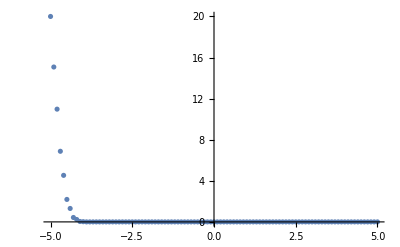

```mathematica
uvec10=uvec;
For[i=1,i≤10,++i,
unew=A.uvec10;
uvec10=unew
];

iter10={};
For[i=1,i≤Length[xvec],++i,
AppendTo[iter10,{xvec[[i]],uvec10[[i]]}]
];

ListPlot[iter10]

(* t = 0.10 *)
```